### Set directory to where you want to save the filters:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bbose/Desktop/ML+ReACT/randpk/random_pk

### Initialize parameters

```mathematica
Nofilt = 500; (*Number of filters to output *)
StartingMod=0.1; (* Initial max modification = 10% *)
StepModk=0.005; (* Max modification for neighbouring k = 0.5% *)
StepModz=0.2; (* Max modification for neighbouring z = 20% *)
Smoothingk=100; (* number of k beyond boundary to modify to have edges smoothed - see averaging later *)
Smoothingz=0 ;
```

```mathematica
planck = ReadList["planck.txt",{Number, Number, Number, Number, Number}];
tabpk=Table[{planck[[i,1]],planck[[i,5]]},{i,1Length[planck]}];
refpk=Interpolation[tabpk];
```

```mathematica
LogLogPlot[refpk[k],{k,0.01,10}];
```

### Define functions determining the k-value as a function of index and the k-error as a function of kval[k]

```mathematica
(*Values of k logarithmically sampled and Gaussian errors *)
(* We work with 500 k bins and 4 z bins *)
mink=0.01;
maxk=10;
Nk=500;

(*Error params *)
nz = 5*10^(-4); (*Shot noise*)
deltak=0.02; (*linear bin width*)
vol = 1.27; (*survey volume in Gpc^3/h^3*)
systematicerr2 = 25; (* Systematic error *)

kval[i_]:= mink * Exp[((i-1)*Log[maxk/mink])/(Nk-1) ];

kerror[k_]:= Sqrt[((2*Pi)/(k*( deltak*vol*1000^3  )^0.5))^2*(refpk[k]+1/nz)^2+systematicerr2]/refpk[k]
```

### For loop to generate multiple random filters -Should we not also change the number of k-bins?

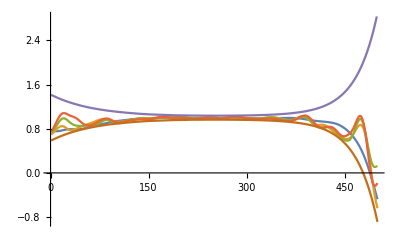

```mathematica
Do[
Clear[kbinw,Nsmooth,kIni,zIni,xir];

kbinw = 4+2*Round[j/ 2000];(* Number of bins over which to average when smoothing - see below - should be even. Let's vary between 4 and 20 for 10k examples --i.e 4 steps *)

(* Random walk around the initial array of ones *)
Nsmooth = RandomInteger[{5,40}] ;(* Number of times kbin averaging is done - see below*)
kIni=RandomInteger[499+2*Smoothingk]+1; (* Initial k to modify *)
zIni=RandomInteger[3+2*Smoothingz]+1; (* Initial z to modify *)
xir=RandomReal[{1,4}] ;(* Xi^2_reduced to be obtained by the modification *)

(* Initialise the filter and set first modification away from 1*)
Clear[Filter,ϵ,FilterSmooth,FilterSmooth2];

Filter[kIni,zIni]=1+StartingMod*RandomReal[{-1,1}];

(* Modify initial k at all neighbouring redshifts in upward direction (Zini to Zmax) *)
For[z=zIni+1,z<(5+2*Smoothingz),
Filter[kIni,z]=Filter[kIni,z-1]+StepModz*RandomReal[{-1,1}];
z=z+1
];

(*  Modify initial k at all neighbouring redshifts in downward direction (Zini to Zmin)  *)
For[z=zIni-1,z>0,
Filter[kIni,z]=Filter[kIni,z+1]+StepModz*RandomReal[{-1,1}];
z=z-1
];

(* Modify k at all neighbouring k in upward direction (kini to kmax + some smoothing scale) for all redshifts *)
For[k=kIni+1,k<(501+2*Smoothingk),
Filter[k,zIni]=Filter[k-1,zIni]+StepModk*RandomReal[{-1,1}];
For[z=zIni+1,z<(5+2*Smoothingz),
Filter[k,z]=Filter[k,z-1]+StepModz*RandomReal[{-1,1}];
z=z+1
];
For[z=zIni-1,z>0,
Filter[k,z]=Filter[k,z+1]+StepModz*RandomReal[{-1,1}];
z=z-1
];
k++
];

(* Modify k at all neighbouring k in downward direction (kini to kmin) for all redshifts *)
For[k=kIni-1,k>0,
Filter[k,zIni]=Filter[k+1,zIni]+StepModk*RandomReal[{-1,1}];
For[z=zIni+1,z<(5+2*Smoothingz),
Filter[k,z]=Filter[k,z-1]+StepModz*RandomReal[{-1,1}];
z=z+1
];
For[z=zIni-1,z>0,
Filter[k,z]=Filter[k,z+1]+StepModz*RandomReal[{-1,1}];
z=z-1
];
k=k-1
];




(* Apply a averaging to the filter across a specificed number of k-bins, and repeat N times - tune to introduce oscillations in the filter at low k *)

For[n=1,n<Nsmooth,
For[z=1,z<5,
For[k=kbinw+1,k<501+2*Smoothingk-kbinw,
Filter[k,z]=Sum[Filter[l,z],{l,k-kbinw/2,k+kbinw/2}]/Sum[1,{l,k-kbinw/2,k+kbinw/2}];
k++];
z++ ];
n++] ;

(* Populate the Filter at indices 1-500 with smoothed result since above loop starts at kbinw*)
For[z=1,z<5,
For[k=1,k<501,
FilterSmooth[k,z]=Filter[Smoothingk+k-1,z];
k++];
z++];


(* Constrain the filter to generate samples with reduced xi^2 between 1 and 4 in this case - see xir parameter*)

myp [z_]:=( (xir^2*500)/Sum[  (FilterSmooth[k,z]-1)^2, { k ,1, 500  } ])^0.5;

ϵ[k_,z_]:=myp[z]*kerror[kval[k]];

For[z=1,z<5,
For[k=1,k<501,
FilterSmooth2[k_,z_ ]:=ϵ[k,z]*(FilterSmooth[k,z ]-1)+1; 
k++];
z++];


(* Collect the filter for each redshift into a single table of dimension (500, 4) *)
RandomFilter =Table[{kval[k],FilterSmooth2[k,1], FilterSmooth2[k,2], FilterSmooth2[k,3], FilterSmooth2[k,4]},{k,1,500}]; 

Export["filters/"<> ToString[j]<>".txt" , RandomFilter  , "Table"  , "FieldSeparators"->" "];

,{ j, Nofilt}] (*Specify how many random filters you want to generate*)
(*2500 + 500*)
ListPlot[{Table[{k,FilterSmooth2[k,1]},{k,1,500}],Table[{k,FilterSmooth2[k,2]},{k,1,500}],Table[{k,FilterSmooth2[k,3]},{k,1,500}],Table[{k,FilterSmooth2[k,4]},{k,1,500}],Table[{k,1+3*kerror[kval[k]]},   {k,1,499}], Table[{k,1-3*kerror[kval[k]]},   {k,1,500}]},Joined->True,PlotRange->All]
```

### Plot the spectra

```mathematica
(*Load spectra once filters have been applied*) 
pofk = ReadList["output/4423.txt",{Number, Number, Number, Number, Number}];
planck = ReadList["planck.txt",{Number, Number, Number, Number, Number}];
tabpk[z_]:=Table[{pofk[[i,1]],pofk[[i,z+1]]},{i,1Length[pofk]}]
tabplanck[z_]:=Table[{planck[[i,1]],planck[[i,z+1]]},{i,1Length[planck]}]
```

```mathematica
errtab[z_]:=Table[{pofk[[i,1]],pofk[[i,z+1]]*kerror[kval[i]]+pofk[[i,z+1]]},{i,1Length[pofk]}]
```

```mathematica
pz15=Interpolation[tabpk[1]];
pz08=Interpolation[tabpk[2]];
pz05=Interpolation[tabpk[3]];
pz01=Interpolation[tabpk[4]];
lcdm15=Interpolation[tabplanck[1]];
lcdm08=Interpolation[tabplanck[2]];
lcdm05=Interpolation[tabplanck[3]];
lcdm01=Interpolation[tabplanck[4]];
```

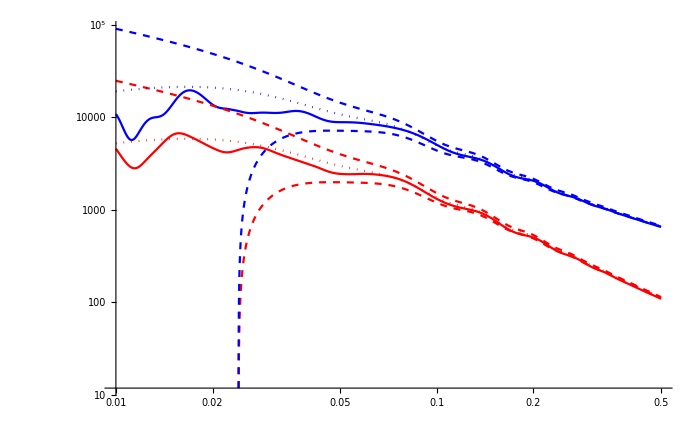

```mathematica
LogLogPlot[{pz15[k],pz01[k],lcdm15[k],lcdm15[k]*(1+3*kerror[k]),lcdm15[k]*(1-3*kerror[k]),lcdm01[k],lcdm01[k]*(1+3*kerror[k]),lcdm01[k]*(1-3*kerror[k])},{k,0.01,0.5},PlotStyle->{Red,Blue,{Red,Dotted},{Red,Dashed},{Red,Dashed},{Blue,Dotted},{Blue,Dashed},{Blue,Dashed}}]
```

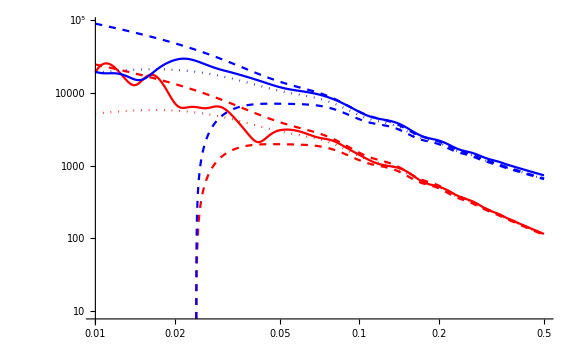

```mathematica
Show[%865,ImageSize->Large]
```

```mathematica
Export["/Users/bbose/Desktop/spectra.png",%866,"PNG"]
```

/Users/bbose/Desktop/spectra.png